## Four-Beam Model

This nodebook calculated the formalism of the four-beam model with neutrino self-interactions.

We use the following definitions

λ=√2 G_F n_e
η=1 for neutrinos, -1 for anti-neutrinos
ω_v=|Δm^2/2E|  is the vacuum frequency without the signs
μ=√2 G_F n_ν_e
n_((ν̄)_e)=α n_ν_e

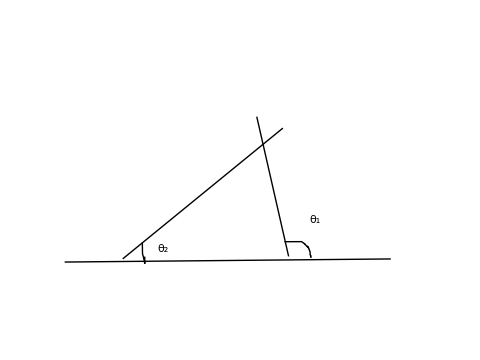
The system can be determined by defining each beam
(ρ,θ,α)

For simplicity,we define the angles to be 

-Graphics-

The System

```mathematica
deltaList={(δ^L)[x],(δ^LB)[x],(δ^R)[x],(δ^RB)[x]}
alphaList={1,α,α,1}
thetaList={Subscript[θ, 1],Subscript[θ, 2],Pi-Subscript[θ, 2],Pi-Subscript[θ, 1]}
```

{δ^L[x],δ^LB[x],δ^R[x],δ^RB[x]}

{1,α,α,1}

{θ_1,θ_2,π-θ_2,π-θ_1}

```mathematica
rhoList=Table[{{1,deltaList[[i]]},{Conjugate[deltaList[[i]]],0}},
{i,1,Length@deltaList}]
```

{{{1,δ^L[x]},{Conjugate[δ^L[x]],0}},{{1,δ^LB[x]},{Conjugate[δ^LB[x]],0}},{{1,δ^R[x]},{Conjugate[δ^R[x]],0}},{{1,δ^RB[x]},{Conjugate[δ^RB[x]],0}}}

```mathematica
hamilv=-1/2 η Subscript[ω, v] PauliMatrix[3]
hamilm=1/2 λ PauliMatrix[3]
```

{{-(η ω_v)/2,0},{0,(η ω_v)/2}}

{{λ/2,0},{0,-λ/2}}

```mathematica
hamilnu[listofdeltas_,listofthetas_,listofalphas_]:=Module[{lenM,alphaM,thetaM},
lenM=Length@listofdeltas;
alphaM=listofalphas;
thetaM=listofthetas;

Table[
Total@Table[μ alphaM[[  Mod[i,4,1]  ]] (1-Cos[  thetaM[[n]] - thetaM[[  Mod[i,4,1]  ]]   ]) rhoList[[  Mod[i,4,1]  ]],
{i,n,n+lenM}],
{n,1,lenM}]

]
```

```mathematica
hamilnu[deltaList,thetaList,alphaList][[1]]//MatrixForm
```

(μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2]) | α μ (1-Cos[θ_1-θ_2]) δ^LB[x]+α μ (1+Cos[θ_1+θ_2]) δ^R[x]+μ (1+Cos[2 θ_1]) δ^RB[x]
μ Conjugate[δ^RB[x]] (1+Cos[2 θ_1])+α μ Conjugate[δ^LB[x]] (1-Cos[θ_1-θ_2])+α μ Conjugate[δ^R[x]] (1+Cos[θ_1+θ_2]) | 0)

## Equation of Motion

```mathematica
hamil=Table[
hamilm+hamilv+hamilnu[deltaList,thetaList,alphaList][[i]],
{i,1,Length@deltaList}];
```

```mathematica
Commutator[a_,b_]:=a.b-b.a;
```

```mathematica
Commutator[hamil[[1]],rhoList[[1]]]//FullSimplify;
%//MatrixForm
```

(μ (-2 Conjugate[δ^RB[x]] Cos[θ_1]^2+α Conjugate[δ^LB[x]] (-1+Cos[θ_1-θ_2])-α Conjugate[δ^R[x]] (1+Cos[θ_1+θ_2])) δ^L[x]+μ Conjugate[δ^L[x]] ((α-α Cos[θ_1-θ_2]) δ^LB[x]+α (1+Cos[θ_1+θ_2]) δ^R[x]+2 Cos[θ_1]^2 δ^RB[x]) | 1/2 (2 (λ+μ+2 α μ+μ Cos[2 θ_1]-2 α μ Sin[θ_1] Sin[θ_2]-η ω_v) δ^L[x]+2 μ (α (-1+Cos[θ_1-θ_2]) δ^LB[x]-α (1+Cos[θ_1+θ_2]) δ^R[x]-2 Cos[θ_1]^2 δ^RB[x]))
μ (2 Conjugate[δ^RB[x]] Cos[θ_1]^2-α Conjugate[δ^LB[x]] (-1+Cos[θ_1-θ_2])+α Conjugate[δ^R[x]] (1+Cos[θ_1+θ_2]))-Conjugate[δ^L[x]] (λ+μ+2 α μ+μ Cos[2 θ_1]-2 α μ Sin[θ_1] Sin[θ_2]-η ω_v) | μ (2 Conjugate[δ^RB[x]] Cos[θ_1]^2-α Conjugate[δ^LB[x]] (-1+Cos[θ_1-θ_2])+α Conjugate[δ^R[x]] (1+Cos[θ_1+θ_2])) δ^L[x]+μ Conjugate[δ^L[x]] (α (-1+Cos[θ_1-θ_2]) δ^LB[x]-α (1+Cos[θ_1+θ_2]) δ^R[x]-2 Cos[θ_1]^2 δ^RB[x]))

Amazingly we find that the diagonal elements are all second orders. Thus this method is self-consistant, since we assumed that the diagonal elements on the LHS, i.e., density matrix, are higher than first order.
Wonderful! We only need one equation for each beam. The equation can be simply extracted by taking out the [[1,2]] components of both sides.

```mathematica
Table[
I D[  rhoList[[i]]  ,x][[1,2]] == Commutator[hamil[[i]],rhoList[[i]]][[1,2]],
{i,1,Length@deltaList}];
%//MatrixForm
```

(ⅈ (δ^L)'[x]==(λ/2+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-(η ω_v)/2) δ^L[x]-(-λ/2+(η ω_v)/2) δ^L[x]-α μ (1-Cos[θ_1-θ_2]) δ^LB[x]-α μ (1+Cos[θ_1+θ_2]) δ^R[x]-μ (1+Cos[2 θ_1]) δ^RB[x]
ⅈ (δ^LB)'[x]==-μ (1-Cos[θ_1-θ_2]) δ^L[x]+(λ/2+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-(η ω_v)/2) δ^LB[x]-(-λ/2+(η ω_v)/2) δ^LB[x]-α μ (1+Cos[2 θ_2]) δ^R[x]-μ (1+Cos[θ_1+θ_2]) δ^RB[x]
ⅈ (δ^R)'[x]==-μ (1+Cos[θ_1+θ_2]) δ^L[x]-α μ (1+Cos[2 θ_2]) δ^LB[x]+(λ/2+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-(η ω_v)/2) δ^R[x]-(-λ/2+(η ω_v)/2) δ^R[x]-μ (1-Cos[θ_1-θ_2]) δ^RB[x]
ⅈ (δ^RB)'[x]==-μ (1+Cos[2 θ_1]) δ^L[x]-α μ (1+Cos[θ_1+θ_2]) δ^LB[x]-α μ (1-Cos[θ_1-θ_2]) δ^R[x]+(λ/2+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-(η ω_v)/2) δ^RB[x]-(-λ/2+(η ω_v)/2) δ^RB[x])

We can make it a matrix equation

```mathematica
rhs=Table[
Commutator[hamil[[i]],rhoList[[i]]][[1,2]],
{i,1,Length@deltaList}]
```

{(λ/2+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-(η ω_v)/2) δ^L[x]-(-λ/2+(η ω_v)/2) δ^L[x]-α μ (1-Cos[θ_1-θ_2]) δ^LB[x]-α μ (1+Cos[θ_1+θ_2]) δ^R[x]-μ (1+Cos[2 θ_1]) δ^RB[x],-μ (1-Cos[θ_1-θ_2]) δ^L[x]+(λ/2+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-(η ω_v)/2) δ^LB[x]-(-λ/2+(η ω_v)/2) δ^LB[x]-α μ (1+Cos[2 θ_2]) δ^R[x]-μ (1+Cos[θ_1+θ_2]) δ^RB[x],-μ (1+Cos[θ_1+θ_2]) δ^L[x]-α μ (1+Cos[2 θ_2]) δ^LB[x]+(λ/2+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-(η ω_v)/2) δ^R[x]-(-λ/2+(η ω_v)/2) δ^R[x]-μ (1-Cos[θ_1-θ_2]) δ^RB[x],-μ (1+Cos[2 θ_1]) δ^L[x]-α μ (1+Cos[θ_1+θ_2]) δ^LB[x]-α μ (1-Cos[θ_1-θ_2]) δ^R[x]+(λ/2+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-(η ω_v)/2) δ^RB[x]-(-λ/2+(η ω_v)/2) δ^RB[x]}

```mathematica
Table[i*j,{i,1,2},{j,10,11}]//MatrixForm
```

(10 | 11
20 | 22)

```mathematica
rhsMatrix=Table[Coefficient[rhs[[i]],deltaList[[j]]],{i,1,Length@deltaList},{j,1,Length@deltaList}];
```

```mathematica
rhsMatrix//MatrixForm
```

(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v | -α μ (1-Cos[θ_1-θ_2]) | -α μ (1+Cos[θ_1+θ_2]) | -μ (1+Cos[2 θ_1])
-μ (1-Cos[θ_1-θ_2]) | λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v | -α μ (1+Cos[2 θ_2]) | -μ (1+Cos[θ_1+θ_2])
-μ (1+Cos[θ_1+θ_2]) | -α μ (1+Cos[2 θ_2]) | λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v | -μ (1-Cos[θ_1-θ_2])
-μ (1+Cos[2 θ_1]) | -α μ (1+Cos[θ_1+θ_2]) | -α μ (1-Cos[θ_1-θ_2]) | λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)

```mathematica
rhsMatrix.deltaList-rhs//FullSimplify
```

{0,0,0,0}

```mathematica
(* Then the equation we are solving becomes simply a linear equation *)
I D[deltaList,x] ==rhsMatrix.deltaList
```

{ⅈ (δ^L)'[x],ⅈ (δ^LB)'[x],ⅈ (δ^R)'[x],ⅈ (δ^RB)'[x]}=={(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) δ^L[x]-α μ (1-Cos[θ_1-θ_2]) δ^LB[x]-α μ (1+Cos[θ_1+θ_2]) δ^R[x]-μ (1+Cos[2 θ_1]) δ^RB[x],-μ (1-Cos[θ_1-θ_2]) δ^L[x]+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) δ^LB[x]-α μ (1+Cos[2 θ_2]) δ^R[x]-μ (1+Cos[θ_1+θ_2]) δ^RB[x],-μ (1+Cos[θ_1+θ_2]) δ^L[x]-α μ (1+Cos[2 θ_2]) δ^LB[x]+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) δ^R[x]-μ (1-Cos[θ_1-θ_2]) δ^RB[x],-μ (1+Cos[2 θ_1]) δ^L[x]-α μ (1+Cos[θ_1+θ_2]) δ^LB[x]-α μ (1-Cos[θ_1-θ_2]) δ^R[x]+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) δ^RB[x]}

Equilibrium Lines, Stability, and Fixed Points

Some ideas here.

About equilibrium points,

1. delta=0 is always an equilibrium point. If the matrix is invertible, this is the only equilibrium point
2.

```mathematica
rhsMatrix//MatrixForm
Inverse[rhsMatrix]//MatrixForm
```

(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v | -α μ (1-Cos[θ_1-θ_2]) | -α μ (1+Cos[θ_1+θ_2]) | -μ (1+Cos[2 θ_1])
-μ (1-Cos[θ_1-θ_2]) | λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v | -α μ (1+Cos[2 θ_2]) | -μ (1+Cos[θ_1+θ_2])
-μ (1+Cos[θ_1+θ_2]) | -α μ (1+Cos[2 θ_2]) | λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v | -μ (1-Cos[θ_1-θ_2])
-μ (1+Cos[2 θ_1]) | -α μ (1+Cos[θ_1+θ_2]) | -α μ (1-Cos[θ_1-θ_2]) | λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)

((α μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1+Cos[2 θ_2]) (1+Cos[θ_1+θ_2])-μ (1-Cos[θ_1-θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-α μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-α^2 μ^2 (1+Cos[2 θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)^2))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (-α μ (1-Cos[θ_1-θ_2]) (α μ^2 (1-Cos[θ_1-θ_2])^2-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2]))+α μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-α^2 μ^2 (1+Cos[2 θ_2]) (1+Cos[θ_1+θ_2])-α μ (1-Cos[θ_1-θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (-α μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)+α μ (1-Cos[θ_1-θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))))
(-α μ (1-Cos[θ_1-θ_2]) (μ^2 (1-Cos[θ_1-θ_2])^2-μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1+Cos[2 θ_2]) (1+Cos[θ_1+θ_2])-μ (1-Cos[θ_1-θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+μ (1+Cos[2 θ_1]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (-μ (1+Cos[2 θ_1]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1-Cos[θ_1-θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1+Cos[θ_1+θ_2])-μ (1-Cos[θ_1-θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1+Cos[θ_1+θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (μ (1+Cos[2 θ_1]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-α μ (1-Cos[θ_1-θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))))
(α μ (1+Cos[θ_1+θ_2]) (μ^2 (1-Cos[θ_1-θ_2])^2-μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1+Cos[2 θ_1]) (-α μ^2 (1+Cos[2 θ_2]) (1+Cos[θ_1+θ_2])-μ (1-Cos[θ_1-θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (μ (1+Cos[2 θ_1]) (α μ^2 (1-Cos[θ_1-θ_2])^2-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2]))-α μ (1+Cos[θ_1+θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1+Cos[θ_1+θ_2])-μ (1-Cos[θ_1-θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (-μ (1+Cos[2 θ_1]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[θ_1+θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))))
(-α μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_2]) (1+Cos[θ_1+θ_2])-μ (1-Cos[θ_1-θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1-Cos[θ_1-θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+μ (1+Cos[2 θ_1]) (-α^2 μ^2 (1+Cos[2 θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)^2))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (-μ (1+Cos[2 θ_1]) (-α^2 μ^2 (1+Cos[2 θ_2]) (1+Cos[θ_1+θ_2])-α μ (1-Cos[θ_1-θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-α μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[θ_1+θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (μ (1+Cos[2 θ_1]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-α μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))) | (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))/(μ (1+Cos[2 θ_1]) (-α μ (1+Cos[2 θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v)))-α μ (1+Cos[θ_1+θ_2]) (-μ (1+Cos[θ_1+θ_2]) (-α μ^2 (1+Cos[2 θ_1]) (1+Cos[2 θ_2])+α μ^2 (1+Cos[θ_1+θ_2])^2)-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+α μ (1-Cos[θ_1-θ_2]) (-μ (1+Cos[θ_1+θ_2]) (α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])+μ (1+Cos[2 θ_1]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-μ^2 (1+Cos[2 θ_1]) (1-Cos[θ_1-θ_2])-μ (1+Cos[θ_1+θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))-μ (1-Cos[θ_1-θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))+(λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v) (-μ (1+Cos[θ_1+θ_2]) (α^2 μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[2 θ_2])+α μ (1+Cos[θ_1+θ_2]) (λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v))+α μ (1+Cos[2 θ_2]) (-α μ^2 (1-Cos[θ_1-θ_2]) (1+Cos[θ_1+θ_2])-α μ (1+Cos[2 θ_2]) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v))+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (-α μ^2 (1-Cos[θ_1-θ_2])^2+(λ+μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[2 θ_2])+μ (1+Cos[θ_1+θ_2])-η ω_v) (λ+μ (1+Cos[2 θ_1])+α μ (1-Cos[θ_1-θ_2])+α μ (1+Cos[θ_1+θ_2])-η ω_v)))))

```mathematica
eigensystem4beams=Eigensystem[rhsMatrix];
```

```mathematica
eigenvalues4beams=Eigenvalues[rhsMatrix]//FullSimplify;
```

```mathematica
eigenvalues4beamsFunction[eta_,lambda_,mu_,theta1_,theta2_,omegav_,alpha_]:=eigenvalues4beams/.{η->eta,λ->lambda,μ->mu,Subscript[θ, 1]->theta1,Subscript[θ, 2]->theta2,Subscript[ω, v]->omegav,α->alpha}

eigensystem4beamsFunction[eta_,lambda_,mu_,theta1_,theta2_,omegav_,alpha_]:=eigensystem4beams/.{η->eta,λ->lambda,μ->mu,Subscript[θ, 1]->theta1,Subscript[θ, 2]->theta2,Subscript[ω, v]->omegav,α->alpha}
```

```mathematica
imPartEigenValues[which_,lambda_,mu_,theta1_,theta2_,alpha_,omegav_:1,imgsize_:600]:=Module[{etaM,lambdaM,muM,theta1M,theta2M,omegavM,alphaM},

Module[{etaM,lambdaM,muM,theta1M,theta2M,omegavM,alphaM},

Manipulate[Grid@{{
"α="<>ToString@alphaM<>"; θ_1="<>ToString[theta1M*180/Pi]<>"°"<>"; θ_2="<>ToString[theta2M*180/Pi]<>"°"},
{
DensityPlot[
-Im@eigenvalues4beamsFunction[etaM,lambdaM,muM,theta1M,theta2M,omegav,alphaM][[which]],
{lambdaM,lambda[[1]],lambda[[2]]},{muM,mu[[1]],mu[[2]]},
ColorFunction->"PigeonTones",PlotLegends->Automatic,FrameLabel->{"λ/ω_v","μ/ω_v"},ImageSize->imgsize]
}},
{{etaM,1,"Hierarchy"},{1,-1}},
{{alphaM,alpha[[2]],"Anti-neutrino Number Density",Appearance->"Open"},alpha[[1,1]],alpha[[1,2]]},
{{theta1M,theta1[[2]],"Neutrino Beam Angle"},theta1[[1,1]],theta1[[1,2]]},
{{theta2M,theta2[[2]],"Neutrino Beam Angle"},theta2[[1,1]],theta2[[1,2]]},
ControlPlacement->Right
]
]
]
```

The inputs are
1. which: which eigenvalue are we looking at, e.g., 1,2,3,4
2. eta: 1, -1 for NH and IH
3. lambda: {a,b} the plot range for lambda
4. mu: {a,b} the plot range for mu
5. theta1: {{a,b},c}, the first element {a,b} is the manipulate range, c is the default value; same for theta2
6. omegav: a number, is one by default
7. alpha: {{a,b},c}, usually negative numbers, because we have chosen to inlcude the sign of anti-neutrinos in alpha.

```mathematica
imPartEigenValues[1,{0,20},{0.5,1.5},{{Pi/8,Pi/3},Pi/4},{{Pi/8,Pi/3},Pi/4},{{-1.5,-0.5},-1}]
```

In fact, the imaginary part exsistance only depends on α, and the angles. The value of it doesn’t depend on the matter effect, since λ only changes the real part of the index Ω.